#### Intensity produced by input and retro fields

The interfering part of the field is written below

```mathematica
field =A Exp[I k z] + B Exp[-I (k z + ϕ)];
interfere = Assuming[ {A>0, B>0, k>0, z>0, ϕ>0}, FullSimplify[ field Conjugate[field]]]
```

A^2+B^2+2 A B Cos[2 k z+ϕ]

```mathematica
interfere = A^2+B^2  -2A B + 4 A B  Cos[k z + ϕ/2]^2
```

A^2-2 A B+B^2+4 A B Cos[k z+ϕ/2]^2

```mathematica
int = interfere /.{A-> √((2 Pin)/(π w0in^2))Exp[ -(x^2+y^2)/w0in^2], B-> √((2 PR α)/(π w0R^2))Exp[ -(x^2+y^2)/w0R^2], C-> √((2 PR (α-1))/(π w0R^2))Exp[ -(x^2+y^2)/w0R^2]}
```

(2 ⅇ^(-(2 (x^2+y^2))/w0in^2) Pin)/(π w0in^2)+(2 ⅇ^(-(2 (x^2+y^2))/w0R^2) PR α)/(π w0R^2)-(4 ⅇ^(-(x^2+y^2)/w0in^2-(x^2+y^2)/w0R^2) √(Pin/w0in^2) √((PR α)/w0R^2))/π+(8 ⅇ^(-(x^2+y^2)/w0in^2-(x^2+y^2)/w0R^2) √(Pin/w0in^2) √((PR α)/w0R^2) Cos[k z+ϕ/2]^2)/π

The non interfering part of the field is

```mathematica
nonint =C^2/.{C-> √((2 PR (1-α))/(π w0R^2))Exp[ -(x^2+y^2)/w0R^2]}
```

(2 ⅇ^(-(2 (x^2+y^2))/w0R^2) PR (1-α))/(π w0R^2)

#### Lattice Depth

In lattice configuration α=1 the intensity is

```mathematica
Expand[(int +nonint )/.{α->1}]
```

(2 ⅇ^(-(2 x^2)/w0in^2-(2 y^2)/w0in^2) Pin)/(π w0in^2)-(4 ⅇ^(-x^2/w0in^2-x^2/w0R^2-y^2/w0in^2-y^2/w0R^2) √(Pin/w0in^2) √(PR/w0R^2))/π+(2 ⅇ^(-(2 x^2)/w0R^2-(2 y^2)/w0R^2) PR)/(π w0R^2)+(8 ⅇ^(-x^2/w0in^2-x^2/w0R^2-y^2/w0in^2-y^2/w0R^2) √(Pin/w0in^2) √(PR/w0R^2) Cos[k z+ϕ/2]^2)/π

```mathematica
Expand[(int +nonint )/.{α->1,x->0,y->0}]
```

(2 Pin)/(π w0in^2)-(4 √(Pin/w0in^2) √(PR/w0R^2))/π+(2 PR)/(π w0R^2)+(8 √(Pin/w0in^2) √(PR/w0R^2) Cos[k z+ϕ/2]^2)/π

The intensity at the center is then

```mathematica
(8 ⅇ^(-x^2/w0in^2-x^2/w0R^2-y^2/w0in^2-y^2/w0R^2) √(Pin/w0in^2) √(PR/w0R^2))/π/.{x->0, y->0}
```

(8 √(Pin/w0in^2) √(PR/w0R^2))/π

And to get the lattice depth in recoils we have to multiply the intensity by π/2 * ItoEr , whre ItoEr = 38709 / 1.4 / 1000   if the powers are in mW and the waists are in um

```mathematica
v0=(8 √(Pin/w0in^2) √(PR/w0R^2))/π π/2 ItoEr
```

4 ItoEr √(Pin/w0in^2) √(PR/w0R^2)

```mathematica
v0 /.{ItoEr ->38709./1.4 /1000.}
```

110.597 √(Pin/w0in^2) √(PR/w0R^2)

NOTE:  If the beams have the same beam waist, then the retro factor is given by

```mathematica
measure={mWEr->22.};
RetroFactor = (w0Input^2 w0Retro^2)/(16 ItoEr^2 mWEr^2)/.{w0Input->47., w0Retro->47., ItoEr->38.709/1.4}/.measure
```

0.824249

#### Radial Frequency in Lattice Configuration

```mathematica
depth = -π/2 ItoU Expand[(int +nonint )/.{α->1,z->0,ϕ->0,y->0}]
```

-1/2 ItoU π ((2 ⅇ^(-(2 x^2)/w0in^2) Pin)/(π w0in^2)+(4 ⅇ^(-x^2/w0in^2-x^2/w0R^2) √(Pin/w0in^2) √(PR/w0R^2))/π+(2 ⅇ^(-(2 x^2)/w0R^2) PR)/(π w0R^2))

```mathematica
Series[ depth, {x,0,2}]
```

(-(ItoU Pin)/w0in^2-2 ItoU √(Pin/w0in^2) √(PR/w0R^2)-(ItoU PR)/w0R^2)+((2 ItoU Pin)/w0in^4+(2 ItoU √(Pin/w0in^2) √(PR/w0R^2))/w0in^2+(2 ItoU PR)/w0R^4+(2 ItoU √(Pin/w0in^2) √(PR/w0R^2))/w0R^2) x^2+O[x]^3

```mathematica
c2=(2 ItoU Pin)/w0in^4+(2 ItoU √(Pin/w0in^2) √(PR/w0R^2))/w0in^2+(2 ItoU PR)/w0R^4+(2 ItoU √(Pin/w0in^2) √(PR/w0R^2))/w0R^2
```

(2 ItoU Pin)/w0in^4+(2 ItoU √(Pin/w0in^2) √(PR/w0R^2))/w0in^2+(2 ItoU PR)/w0R^4+(2 ItoU √(Pin/w0in^2) √(PR/w0R^2))/w0R^2

```mathematica
nu2 = FullSimplify[ 1/(2 π)^2 2 c2/meff] (*in kHZ*)
```

(ItoU (PR w0in^4+(PR √(Pin/w0in^2) w0in^4)/(√(PR/w0R^2))+Pin w0R^4+(Pin √(PR/w0R^2) w0R^4)/(√(Pin/w0in^2))))/(meff π^2 w0in^4 w0R^4)

```mathematica
nu2/.{Pin->PinD,PR-> PinD R}
```

(ItoU (PinD R w0in^4+(PinD R √(PinD/w0in^2) w0in^4)/(√((PinD R)/w0R^2))+PinD w0R^4+(PinD √((PinD R)/w0R^2) w0R^4)/(√(PinD/w0in^2))))/(meff π^2 w0in^4 w0R^4)

The solution for the retro factor R starting from the lattice depth measurement v0 is inserted in nu2

```mathematica
nu2A= nu2/.{Pin->PinD,PR-> PinD R}/.{R->(w0in^2 w0R^2)/(16 ItoEr^2 mWEr^2)}
```

(ItoU ((PinD w0in^6 w0R^2)/(16 ItoEr^2 mWEr^2)+(PinD √(PinD/w0in^2) w0in^6 w0R^2)/(4 ItoEr^2 mWEr^2 √((PinD w0in^2)/(ItoEr^2 mWEr^2)))+PinD w0R^4+(PinD √((PinD w0in^2)/(ItoEr^2 mWEr^2)) w0R^4)/(4 √(PinD/w0in^2))))/(meff π^2 w0in^4 w0R^4)

In this expression we can insert the measured values of  the mW/Er  of the lattice beam, and also the measured values of PinD.

```mathematica
numerical ={ItoEr->38.709/1.4, ItoU->38.709,meff->7.2 10^-4}
measure = {mWEr->18.6,PinD->199.5}
nu2B = FullSimplify[nu2A /.numerical/.measure]
```

{ItoEr→27.6493,ItoU→38.709,meff→0.00072}

{mWEr→18.6,PinD→199.5}

(1.08673×10^6)/w0in^4+(0.256808 w0in^2)/w0R^2+(528.282 √(1/w0in^2) (1. w0in^2+1. w0R^2))/(√(w0in^2) w0R^2)

We can then create a function, which given the value of nu2 and w0in will solve for w0R

```mathematica
RetroWaist[ nu2_, w0IN_]:=Module[{Rsol,w0Retro,ItoEr,mWEr},
w0Retro = Abs[w0R/.NSolve[Evaluate[nu2B/.{w0in->w0IN}]==nu2,w0R][[1]]];

Rsol=(w0Retro^2 w0IN^2)/(16 ItoEr^2 mWEr^2)/.{mWEr->18.6,ItoEr->38.709/1.4};
{w0Retro,Rsol}
]
```

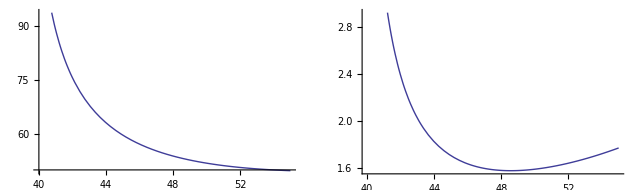

```mathematica
GraphicsGrid[{{Plot[RetroWaist[ 0.82, w0][[1]],{w0,40,55}],Plot[RetroWaist[ 0.82, w0][[2]],{w0,40,55}]}}]
```

```mathematica
RetroWaist[0.82,43.7]
```

64.4323

#### Dimple Frequency

In dimple configuration

```mathematica
depth = -π/2 ItoU Expand[(int +nonint )/.{α->0, y->0}]
```

-1/2 ItoU π ((2 ⅇ^(-(2 x^2)/w0in^2) Pin)/(π w0in^2)+(2 ⅇ^(-(2 x^2)/w0R^2) PR)/(π w0R^2))

```mathematica
Series[ depth, {x,0,2}]
```

(-(ItoU Pin)/w0in^2-(ItoU PR)/w0R^2)+((2 ItoU Pin)/w0in^4+(2 ItoU PR)/w0R^4) x^2+O[x]^3

```mathematica
c2 = (2 ItoU Pin)/w0in^4+(2 ItoU PR)/w0R^4
```

(2 ItoU Pin)/w0in^4+(2 ItoU PR)/w0R^4

We have that 

1/2 m (2 π ν)^2 =  SeriesCoefficient[2]

Now, to put in the mass of lithium we use 

m=6AMU=(6h)/(0.4 um^2 MHz)=(6 48 uK/Mhz)/(0.4 um^2 MHz)=720 uK/(um^2 MHz^2) = 7.2 10^-4 uK/(um^2 kHz^2)⧦ meff

```mathematica
nu = FullSimplify[ 1/(2 π)√(2 c2/meff)] (*in kHZ*)
```

(√((ItoU (Pin/w0in^4+PR/w0R^4))/meff))/π

```mathematica
nu /. {ItoU->38709./1000., meff->7.2 10^-4}
```

73.8057 √(Pin/w0in^4+PR/w0R^4)

#### Combining the trap depth and dimple frequency measurements to estimate the retro beam waist

```mathematica
v0
nu
```

4 ItoEr √(Pin/w0in^2) √(PR/w0R^2)

(√((ItoU (Pin/w0in^4+PR/w0R^4))/meff))/π

At this point we define the retro factor so that PR = Pin R

```mathematica
v0 = v0/.{Pin->PinL, PR-> PinL R}
nu = nu/.{Pin->PinD,PR-> PinD R}
```

4 ItoEr √(PinL/w0in^2) √((PinL R)/w0R^2)

(√((ItoU (PinD/w0in^4+(v0num^2 w0in^2)/(16 ItoEr^2 PinD w0R^2)))/meff))/π

```mathematica
(√((ItoU (Pin/w0in^4+(Pin R)/w0R^4))/meff))/π
```

Here we just write the solutions down explicitly to avoid going through the stuff above every time

```mathematica
v0= 4 ItoEr √(PinL/w0in^2) √((PinL R)/w0R^2)
nu =1/π √((ItoU (PinD/w0in^4+(PinD R)/w0R^4))/meff)
```

4 ItoEr √(PinL/w0in^2) √((PinL R)/w0R^2)

(√((ItoU (PinD/w0in^4+(PinD R)/w0R^4))/meff))/π

We solve the first equation for R

```mathematica
Solve[v0==v0num,{R}]
```

```mathematica
{{R->(v0num^2 w0in^2 w0R^2)/(16 ItoEr^2 PinL^2)}}
```

```mathematica
R=(v0num^2 w0in^2 w0R^2)/(16 ItoEr^2 PinL^2)
```

(v0num^2 w0in^2 w0R^2)/(16 ItoEr^2 PinL^2)

And solve the second one for wR to the fourth power

```mathematica
Solve[ nu2 == 1/π^2(ItoU (PinD/w0in^4+(PinD Rs)/w0R4))/meff, w0R4]
```

{{w0R4→(ItoU PinD Rs w0in^4)/(-ItoU PinD+meff nu2 π^2 w0in^4)}}

We use the solution for R above to find a simpler solution for w0R to the 2nd power

```mathematica
w0R2 = (ItoU PinD w0in^4)/(-ItoU PinD+meff nu2 π^2 w0in^4)(v0num^2 w0in^2)/(16 ItoEr^2 PinL^2)
```

(ItoU PinD v0num^2 w0in^6)/(16 ItoEr^2 PinL^2 (-ItoU PinD+meff nu2 π^2 w0in^4))

```mathematica
w0Rsol= ((ItoU PinD w0in^4)/(-ItoU PinD+meff nu2 π^2 w0in^4)(v0num^2 w0in^2)/(16 ItoEr^2 PinL^2))^(1/2)
```

1/4 √((ItoU PinD v0num^2 w0in^6)/(ItoEr^2 PinL^2 (-ItoU PinD+meff nu2 π^2 w0in^4)))

We plug in all the measurements and the numerical values

{ItoEr→27.6493,ItoU→38.709,meff→0.00072}

{v0num→24.77,PinL→535.5,PinD→326.,nu2→0.56}

1.74922×10^-7 w0in^2 w0R^2

0.0469826 √(w0in^6/(-12619.1+0.00397942 w0in^4))

(3.86118×10^-10 w0in^8)/(-12619.1+0.00397942 w0in^4)

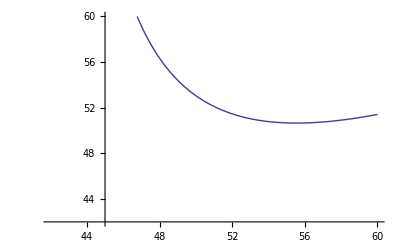

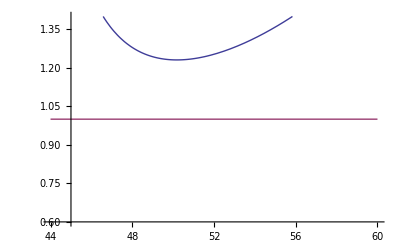

```mathematica
numerical ={ItoEr->38709./1.4/1000., ItoU->38709./1000.,meff->7.2 10^-4}
measure1 ={v0num->24.91, PinL->543.5, PinD->338., nu2->0.49};
measure2 ={v0num->24.77, PinL->535.5, PinD->326., nu2->0.56};
measure=measure2
Clear[v0num, w0in, w0R, ItoEr, ItoU, Rs, meff, PinL, PinD];
Rsol= (v0num^2 w0in^2 w0R^2)/(16 ItoEr^2 PinL^2)/.numerical/.measure
w0Rsol=((ItoU PinD w0in^4)/(-ItoU PinD+meff nu2 π^2 w0in^4)(v0num^2 w0in^2)/(16 ItoEr^2 PinL^2))^(1/2)/.numerical/.measure 
Rsolfull = Rsol/.{w0R->w0Rsol}
Plot[  w0Rsol, {w0in, 42., 60.}, PlotRange->{42.,60.}]
Plot[ {Rsol/.{w0R->w0Rsol},1.}, {w0in, 44. , 60.},PlotRange->{0.6,1.4}]
```

We then plot the solution for w0R and R  as a function of w0in

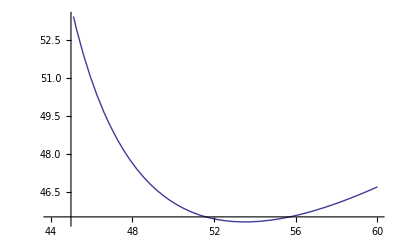

(3.86118×10^-10 w0in^8)/(-12619.1+0.00461897 w0in^4)

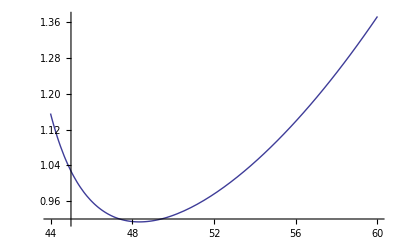

#### Plotting the solutions backwards